```mathematica
u[c_]=(c^(1-1/σ)-1)/(1-1/σ);
f[k_]=A*(α*k^ρ+1-α)^(1/ρ);
r[k_]=D[f[k],k];w[k_]=f[k]-r[k]*k;
```

```mathematica
s[k_,k1_]=s/.Solve[D[u[w[k]-s],s]+β*D[u[r[k1]*s],s]==0,s][[1]];
```

```mathematica
FullSimplify[s[k,k1],Assumptions->{α>0,σ>0,k>0,k1>0,ρ<0,β>0}]
```

-(A k1^(1+ρ σ) (-1+α) (1+(-1+k^ρ) α)^(-1+1/ρ) (1+(-1+k1^ρ) α)^((ρ+σ)/ρ) (A α β)^σ)/(A k1^(ρ+σ) α (1+(-1+k1^ρ) α)^(1/ρ+σ)+k1^(1+ρ σ) (1+(-1+k1^ρ) α)^((ρ+σ)/ρ) (A α β)^σ)

```mathematica
vals={A-> 20,α->1/3,ρ-> -2,β-> 0.3,σ-> 0.1,n->1.097};
```

```mathematica
dk1[k_,k1_]=dk1dk/.Solve[(Simplify[Dt[k1-1/(1+n)*s[k,k1],k,Constants->{α,β,σ,ρ,n,A}]]/.Dt[k1,k,Constants->{A,n,α,β,ρ,σ}]-> dk1dk)==0,dk1dk][[1]];
```

```mathematica
f1k[k_]:=k1/.NSolve[(k1==1/(1+n)*s[k,k1])/.vals,k1,Reals]
```

```mathematica
saving[k_,k1_]=s/.Solve[D[u[w[k]-s],s]+β*D[u[r[k1]*s],s]==0,s][[1]]/.vals
```

(4.76344/(√(2/3+1/(3 k^2)) (2/3+1/(3 k1^2))^0.05 k1^1.2)+(9.52688 k1^0.8)/(√(2/3+1/(3 k^2)) (2/3+1/(3 k1^2))^0.05))/(40/(9 (2/3+1/(3 k1^2))^0.4 k1^1.9)+20/(9 k^2 (2/3+1/(3 k1^2))^0.4 k1^1.9)+0.238172/((2/3+1/(3 k1^2))^0.05 k1^1.2)+0.119086/(k^2 (2/3+1/(3 k1^2))^0.05 k1^1.2)+(0.476344 k1^0.8)/((2/3+1/(3 k1^2))^0.05)+(0.238172 k1^0.8)/(k^2 (2/3+1/(3 k1^2))^0.05))

```mathematica
q=(k1-1/(1+n)*saving[k,k1])/.vals;
```

```mathematica
nxtk[k_]:=k1/.NSolve[(k1-1/(1+n)*saving[k,k1])/.vals,k1,Reals]
```

```mathematica
der[k_,k1_]=Simplify[Dt[k1,k]/.Solve[Dt[q,k]==0,Dt[k1,k]][[1]]];
```

```mathematica
nxtk[1]
```

{0.265636,1.23467,5.8322}

```mathematica
isneg[k_]:=Min[der[1,#]&/@nxtk[k]]
```

```mathematica
negs=isneg/@Table[x,{x,0.1,5,.01}];
```

```mathematica
arenegs=Select[negs,#<0&]
```

{-40.8087,-3.91091,-3.39497,-3.0633,-2.82774,-2.65055,-2.51222,-2.40146,-2.31118,-2.23667,-2.17466,-2.1228,-2.07937,-2.04304,-2.01283,-1.98794,-1.96776,-1.95181,-1.93968,-1.93109,-1.92577,-1.92355,-1.92428,-1.92785,-1.93419,-1.94327,-1.95507,-1.96961,-1.98694,-2.00714,-2.03031,-2.05659,-2.08615,-2.11921,-2.15601,-2.19686,-2.24213,-2.29225,-2.34774,-2.40922,-2.47743,-2.55326,-2.63782,-2.73243,-2.83875,-2.95884,-3.09532,-3.25155,-3.4319,-3.64222,-3.89042,-4.18755,-4.5495,-4.99998,-5.57602,-6.33884,-7.39747,-8.96697,-11.5385,-16.533,-30.4784,-291.488}

```mathematica
ks=Flatten[Position[negs,#]&/@arenegs]
```

{67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128}

```mathematica
mink=Table[x,{x,0.1,5,.01}][[First[ks]]]
```

0.76

```mathematica
maxk=Table[x,{x,0.1,5,.01}][[Last[ks]]]
```

1.37

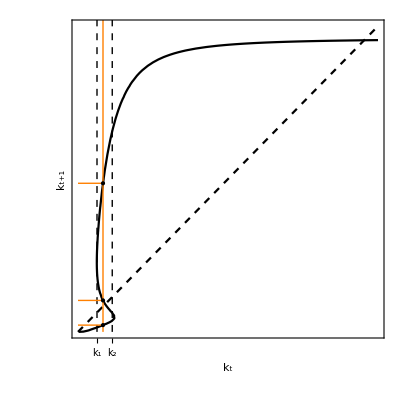

```mathematica
pl1=ContourPlot[{q==p,q==1/(1+1.097)*saving[p,q]},{p,0,12},{q,0,12},FrameLabel->{Subscript["k","t"],Subscript["k","t+1"]},ContourStyle->{{Black,Dashed},Black},Epilog->{{Dashed,Line[{{mink,0},{mink,14}}]},{Dashed,Line[{{maxk,0},{maxk,14}}]},{Orange,Line[{{1,0},{1,14}}]},{Orange,Line[{{0,#},{1,#}}]&/@nxtk[1]},{PointSize[Large],Point[{1,#}]&/@nxtk[1]}},FrameTicks-> {{None,None},{{{mink,Subscript["k",1]},{maxk,Subscript["k",2]}},None}}]
```

```mathematica
Export["/home/eric/eric-roca.github.io/static/img/olg/backwards.png",pl1]
```

/home/eric/eric-roca.github.io/static/img/olg/backwards.png

```mathematica
nxtk[1]
```

{0.265636,1.23467,5.8322}